# Correlations

Plots and tables of correlations between dependent variables. Used for “Changes in filament microstructures during direct ink writing with yield stress fluid support”
Last updated November 2019 by Leanne Friedrich

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
<<"Mathematica\\correlations.wl";
bigtable2 = Import["Tables\\bigtable2_middleedge.csv"];
changetable = Import["Tables\\changetable_middleedge.csv"];
combinetable = Import["Tables\\combinetable_middleedge.csv"];
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

## Create correlation tables

uses constructk (kendall.wl), constructknn (kendall.wl)

### bigtable correlations (these are also split by pass)

```mathematica
ilist = Join[Range[11,29,2], Range[31,55,6], Range[35,59,6]];
kbt = constructk[bigtable2, BIGHEADER2, ilist];
cnn = constructknn[bigtable2, BIGHEADER2, BTNNINDICES, ilist, {"Relaxed position", "Sheared position", "Relaxed width", "Sheared width"}];
Export["Tables\\corrtablebt.csv", Join[kbt, cnn[[2;;]]]];
```

### combined correlations (these are averaged over the three passes)

```mathematica
kcombine = constructk[combinetable, COMBINEHEADER, Join[Range[10, 28, 2], Range[30,48,6], Range[34, 52, 6]]];
Export["Tables\\corrtablecomb.csv", kcombine];
```

## Latex tables

```mathematica
kbt = Import["Tables\\corrtablebt.csv"];
kcombine = Import["Tables\\corrtablecomb.csv"];
```

uses corrtable (correlations.wl)

### vector - vector

#### not averaged over lines

```mathematica
tout = corrtable[kbt, Range[11,29,2],Range[11,29,2], REGIONLIST, REGIONLIST, False]
Export["figures\\vvbtcorr.txt", tout]
```

\centering\begin{tabular}{lcccccccccc}
	 & nozzle & ahead & just behind & behind outer & far behind & behind NN & behind 2NN & outer & NN & 2NN\\
	\multicolumn{11}{l}{\textbf{Layer-by-layer}}\\
	nozzle &  & ++ & - &  &  &  & + & + & + & +\\
	ahead &  &  & - & + &  & - & - & ++ & ++ & +\\
	just behind &  &  &  & + & ++++ & +++ & ++ & ++ & ++ & \\
	behind outer &  &  &  &  & ++ & + & + & ++ & + & ++\\
	far behind &  &  &  &  &  & +++ & ++ & + & ++ & +\\
	behind NN &  &  &  &  &  &  & +++ & + & + & +\\
	behind 2NN &  &  &  &  &  &  &  & + & + & ++\\
	outer &  &  &  &  &  &  &  &  & + & +\\
	NN &  &  &  &  &  &  &  &  &  & +++\\
	2NN &  &  &  &  &  &  &  &  &  & \\
	\multicolumn{11}{l}{\textbf{Bath}}\\
	nozzle &  & + & + & + & + & + &  & + & ++ & +\\
	ahead &  &  & - & + & + & - & - & ++ & +++ & \\
	just behind &  &  &  & ++ & +++ & ++ & + & + & ++ & ++\\
	behind outer &  &  &  &  & + & - - & - - & ++ & + & -\\
	far behind &  &  &  &  &  & ++++ & ++ & ++ & ++ & ++\\
	behind NN &  &  &  &  &  &  & ++++ & + & + & ++\\
	behind 2NN &  &  &  &  &  &  &  & + &  & ++\\
	outer &  &  &  &  &  &  &  &  & + & +\\
	NN &  &  &  &  &  &  &  &  &  & ++\\
	2NN &  &  &  &  &  &  &  &  &  & 
\end{tabular}

figures\vvbtcorr.txt

#### averaged over lines

```mathematica
tout = corrtable[kcombine, Range[10,28,2],Range[10,28,2], REGIONLIST, REGIONLIST, False]
Export["figures\\vvavecorr.txt", tout]
```

\centering\begin{tabular}{lcccccccccc}
	 & nozzle & ahead & just behind & behind outer & far behind & behind NN & behind 2NN & outer & NN & 2NN\\
	\multicolumn{11}{l}{\textbf{Layer-by-layer}}\\
	nozzle &  & ++ & - &  &  &  & + &  & ++ & ++\\
	ahead &  &  &  & ++ &  & - &  & ++ & ++ & +\\
	just behind &  &  &  & ++ & ++++ & +++ & + & ++ & +++ & ++\\
	behind outer &  &  &  &  & +++ & + & ++ & +++ & + & +\\
	far behind &  &  &  &  &  & +++ & ++ & + & +++ & ++\\
	behind NN &  &  &  &  &  &  & +++ & + & ++ & ++\\
	behind 2NN &  &  &  &  &  &  &  &  & + & ++\\
	outer &  &  &  &  &  &  &  &  & + & +\\
	NN &  &  &  &  &  &  &  &  &  & +++\\
	2NN &  &  &  &  &  &  &  &  &  & \\
	\multicolumn{11}{l}{\textbf{Bath}}\\
	nozzle &  &  & ++ &  & + & + &  & + & ++ & +\\
	ahead &  &  & - & + & + & - & - & ++ & ++ & \\
	just behind &  &  &  & ++ & ++++ & ++ & + & ++ & +++ & ++\\
	behind outer &  &  &  &  & + & - - & - - - & + &  & -\\
	far behind &  &  &  &  &  & +++++ & +++ & ++ & ++ & ++\\
	behind NN &  &  &  &  &  &  & +++++ & + & + & ++\\
	behind 2NN &  &  &  &  &  &  &  & + &  & ++\\
	outer &  &  &  &  &  &  &  &  & + & +\\
	NN &  &  &  &  &  &  &  &  &  & +++\\
	2NN &  &  &  &  &  &  &  &  &  & 
\end{tabular}

figures\vvavecorr.txt

### dist-dist

```mathematica
DeleteDuplicates[Select[kbt, #[[1]]>72&][[;;,{1,3}]]]
```

{{73,Relaxed position},{74,Sheared position},{75,Relaxed width}}

#### absolute position-width, not averaged over lines

```mathematica
tout = corrtable[kbt, {31,49, 55, 74}, {35, 53, 59, 76} , {"Initial position", "Relaxed position NN", "Relaxed position 2nd NN", "Sheared position"}, {"Initial width", "Relaxed width NN", "Relaxed width 2nd NN", "Sheared width"}, False]
Export["figures\\poswidthcorrabs.txt", tout]
```

\centering\begin{tabular}{lcccc}
	 & Initial position & Relaxed position NN & Relaxed position 2nd NN & Sheared position\\
	\multicolumn{5}{l}{\textbf{Layer-by-layer}}\\
	Initial width &  &  & - & -\\
	Relaxed width NN & - - & - & - - - & - -\\
	Relaxed width 2nd NN & + &  & - - - & \\
	Sheared width & - - &  & - & - -\\
	\multicolumn{5}{l}{\textbf{Bath}}\\
	Initial width & ++ & + & - & ++\\
	Relaxed width NN &  &  & - & \\
	Relaxed width 2nd NN & - - & - - & - - - - & - -\\
	Sheared width & - - & - & - & - -
\end{tabular}

figures\poswidthcorrabs.txt

#### absolute position-position, not averaged over lines

```mathematica
tout = corrtable[kbt, {31,49, 55, 74}, {31,49, 55, 74} , {"Initial position", "Relaxed position NN", "Relaxed position 2nd NN", "Sheared position"}, {"Initial position", "Relaxed position NN", "Relaxed position 2nd NN", "Sheared position"}, False]
Export["figures\\posposcorrabs.txt", tout]
```

\centering\begin{tabular}{lcccc}
	 & Initial position & Relaxed position NN & Relaxed position 2nd NN & Sheared position\\
	\multicolumn{5}{l}{\textbf{Layer-by-layer}}\\
	Initial position &  & +++ & ++ & +++++++\\
	Relaxed position NN &  &  & +++++ & +++\\
	Relaxed position 2nd NN &  &  &  & ++\\
	Sheared position &  &  &  & \\
	\multicolumn{5}{l}{\textbf{Bath}}\\
	Initial position &  & ++ & ++ & ++++++\\
	Relaxed position NN &  &  & ++++++ & ++\\
	Relaxed position 2nd NN &  &  &  & ++\\
	Sheared position &  &  &  & 
\end{tabular}

figures\posposcorrabs.txt

#### absolute width-width, not averaged over lines

```mathematica
tout = corrtable[kbt, {35, 53, 59, 76}, {35, 53, 59, 76} , {"Initial width", "Relaxed width NN", "Relaxed width 2nd NN", "Sheared width"}, {"Initial width", "Relaxed width NN", "Relaxed width 2nd NN", "Sheared width"}, False]
Export["figures\\widthwidthcorrabs.txt", tout]
```

\centering\begin{tabular}{lcccc}
	 & Initial width & Relaxed width NN & Relaxed width 2nd NN & Sheared width\\
	\multicolumn{5}{l}{\textbf{Layer-by-layer}}\\
	Initial width &  & +++ & ++ & +++\\
	Relaxed width NN &  &  & ++ & +++\\
	Relaxed width 2nd NN &  &  &  & ++\\
	Sheared width &  &  &  & \\
	\multicolumn{5}{l}{\textbf{Bath}}\\
	Initial width &  & +++ & ++ & ++\\
	Relaxed width NN &  &  & ++ & ++\\
	Relaxed width 2nd NN &  &  &  & ++\\
	Sheared width &  &  &  & 
\end{tabular}

figures\widthwidthcorrabs.txt

#### relative position-width, averaged over lines

```mathematica
distproglist = Flatten[Table[Table[j[[1]]<>i[[1]]<>j[[2]]<>i[[2]],{j,{{"Initial ", ""}, {"$\\Delta$"," relax NN"} , {"$\\Delta$"," relax 2nd NN"}, {"$\\Delta$"," shear"}}}],{i, {{"pos", ""}, {"width", ""}}}]];
tout = corrtable[kcombine,Range[30,48,6],Range[34, 52, 6], distproglist[[1;;4]], distproglist[[5;;]],False]
Export["figures\\poswidthcorrrel.txt", tout]
```

\centering\begin{tabular}{lcccc}
	 & Initial pos & $\Delta$pos relax NN & $\Delta$pos relax 2nd NN & $\Delta$pos shear\\
	\multicolumn{5}{l}{\textbf{Layer-by-layer}}\\
	Initial width & - - & ++ & ++ & -\\
	$\Delta$width relax NN &  &  & - - & +\\
	$\Delta$width relax 2nd NN & ++ & - & - - - & ++\\
	$\Delta$width shear & - &  & ++ & - -\\
	\multicolumn{5}{l}{\textbf{Bath}}\\
	Initial width & ++ &  & - - & +\\
	$\Delta$width relax NN & - - &  & + & \\
	$\Delta$width relax 2nd NN & ++ & - - & - - - & ++\\
	$\Delta$width shear & - - & + & ++ & - -
\end{tabular}

figures\poswidthcorrrel.txt

#### relative position-position, averaged over lines

```mathematica
distproglist = Flatten[Table[Table[j[[1]]<>i[[1]]<>j[[2]]<>i[[2]],{j,{{"Initial ", ""}, {"$\\Delta$"," relax NN"} , {"$\\Delta$"," relax 2nd NN"}, {"$\\Delta$"," shear"}}}],{i, {{"pos", ""}, {"width", ""}}}]];
tout = corrtable[kcombine,Range[30,48,6],Range[30,48,6], distproglist[[1;;4]],distproglist[[1;;4]],False]
Export["figures\\posposcorrrel.txt", tout]
```

\centering\begin{tabular}{lcccc}
	 & Initial pos & $\Delta$pos relax NN & $\Delta$pos relax 2nd NN & $\Delta$pos shear\\
	\multicolumn{5}{l}{\textbf{Layer-by-layer}}\\
	Initial pos &  & - - - - - - & - - - - & +++\\
	$\Delta$pos relax NN &  &  & ++++ & - - - - -\\
	$\Delta$pos relax 2nd NN &  &  &  & - - - - -\\
	$\Delta$pos shear &  &  &  & \\
	\multicolumn{5}{l}{\textbf{Bath}}\\
	Initial pos &  & - - - - & - - - & +++\\
	$\Delta$pos relax NN &  &  & +++++ & - - - - -\\
	$\Delta$pos relax 2nd NN &  &  &  & - - - - - -\\
	$\Delta$pos shear &  &  &  & 
\end{tabular}

figures\posposcorrrel.txt

#### relative width-width, averaged over lines

```mathematica
distproglist = Flatten[Table[Table[j[[1]]<>i[[1]]<>j[[2]]<>i[[2]],{j,{{"Initial ", ""}, {"$\\Delta$"," relax NN"} , {"$\\Delta$"," relax 2nd NN"}, {"$\\Delta$"," shear"}}}],{i, {{"pos", ""}, {"width", ""}}}]];
tout = corrtable[kcombine,Range[34, 52, 6],Range[34, 52, 6], distproglist[[5;;]], distproglist[[5;;]],False]
Export["figures\\widthwidthcorrrel.txt", tout]
```

\centering\begin{tabular}{lcccc}
	 & Initial width & $\Delta$width relax NN & $\Delta$width relax 2nd NN & $\Delta$width shear\\
	\multicolumn{5}{l}{\textbf{Layer-by-layer}}\\
	Initial width &  & - - - - & - - & -\\
	$\Delta$width relax NN &  &  & +++ & - - -\\
	$\Delta$width relax 2nd NN &  &  &  & - - - - -\\
	$\Delta$width shear &  &  &  & \\
	\multicolumn{5}{l}{\textbf{Bath}}\\
	Initial width &  & - - - - &  & - -\\
	$\Delta$width relax NN &  &  & ++ & - - -\\
	$\Delta$width relax 2nd NN &  &  &  & - - - - - -\\
	$\Delta$width shear &  &  &  & 
\end{tabular}

figures\widthwidthcorrrel.txt

### vector-distribution

#### vector - absolute distribution

```mathematica
distlist = {"Initial position", "Relaxed position NN", "Relaxed position 2nd NN", "Sheared position","Initial width", "Relaxed width NN", "Relaxed width 2nd NN", "Sheared width"};
tout = corrtable[kbt, Range[11, 29, 2], {31,49, 55, 74, 35, 53, 59, 76} , REGIONLIST, distlist,False]
Export["figures\\vdistcorrabs.txt", tout]
```

\centering\begin{tabular}{lcccccccccc}
	 & nozzle & ahead & just behind & behind outer & far behind & behind NN & behind 2NN & outer & NN & 2NN\\
	\multicolumn{11}{l}{\textbf{Layer-by-layer}}\\
	Initial position & + & + &  & + & - & - & - & + & - & -\\
	Relaxed position NN &  & + & + & + &  &  &  & ++ &  & \\
	Relaxed position 2nd NN &  &  & + &  &  &  &  & ++ & + & \\
	Sheared position & - &  &  & + & - & - & - & + & - & -\\
	Initial width & - & + & - & ++ &  &  & + &  &  & +\\
	Relaxed width NN &  &  & + & + & + &  &  & - &  & +\\
	Relaxed width 2nd NN &  &  &  & + &  &  &  &  &  & \\
	Sheared width &  &  &  & + & + & + & + & - &  & +\\
	\multicolumn{11}{l}{\textbf{Bath}}\\
	Initial position &  & - &  & + & + & + & + & + & - & -\\
	Relaxed position NN & - & - &  & + &  &  &  &  & - & +\\
	Relaxed position 2nd NN & - & - &  & - &  & + & ++ &  &  & +\\
	Sheared position &  & - &  & + &  & + &  &  & - & -\\
	Initial width &  & + & + & +++ & + & - - & - - & - & + & -\\
	Relaxed width NN & - & + &  & ++ &  & - & - - & - - & + & -\\
	Relaxed width 2nd NN &  & + & + & + & + &  & - - &  & ++ & \\
	Sheared width &  & + & - &  &  & - & - & - & + & 
\end{tabular}

figures\vdistcorrabs.txt

#### vector - relative distribution

```mathematica
distproglist = Flatten[Table[Table[j[[1]]<>i[[1]]<>j[[2]]<>i[[2]],{j,{{"Initial ", ""}, {"$\\Delta$"," relax NN"} , {"$\\Delta$"," relax 2nd NN"}, {"$\\Delta$"," shear"}}}],{i, {{"pos", ""}, {"width", ""}}}]];
tout = corrtable[kcombine, Range[10, 28, 2], Join[Range[30,48,6], Range[34, 52, 6]], REGIONLIST, distproglist, False]
Export["figures\\vdistcorrrel.txt", tout]
```

\centering\begin{tabular}{lcccccccccc}
	 & nozzle & ahead & just behind & behind outer & far behind & behind NN & behind 2NN & outer & NN & 2NN\\
	\multicolumn{11}{l}{\textbf{Layer-by-layer}}\\
	Initial pos & + & ++ & - &  & - & - & - & ++ &  & \\
	$\Delta$pos relax NN & - &  & + & + & + & + & + &  &  & \\
	$\Delta$pos relax 2nd NN &  & - & + & + & + & ++ & + & + & + & \\
	$\Delta$pos shear &  &  & - &  & - & - & - & - & - & -\\
	Initial width & - & + &  & +++ & + & + & + & + &  & \\
	$\Delta$width relax NN & + &  &  & - - & + &  &  & - &  & \\
	$\Delta$width relax 2nd NN &  & + &  &  &  & - & - & + &  & \\
	$\Delta$width shear &  & - &  & - &  & + &  & - &  & +\\
	\multicolumn{11}{l}{\textbf{Bath}}\\
	Initial pos &  & - &  & + & + & + & + & + & - - & -\\
	$\Delta$pos relax NN & - &  &  &  & - & - &  & - & + & ++\\
	$\Delta$pos relax 2nd NN & - &  &  & - - &  & + & + & + &  & ++\\
	$\Delta$pos shear & + &  &  &  &  &  &  &  &  & - -\\
	Initial width &  & + & + & +++ & + & - - & - - & - & ++ & -\\
	$\Delta$width relax NN & - & - & - & - - & - &  &  &  & - - & \\
	$\Delta$width relax 2nd NN &  &  & + & ++ &  & - & - & + &  & -\\
	$\Delta$width shear & + &  & - & - - &  & ++ & ++ &  & + & ++
\end{tabular}

figures\vdistcorrrel.txt

## Correlation plots

correlations.wl functions: tplist, tplist2, ticksfunc, plotlist, pl2grid, plotijgrid, absdist, reldist
master.wl functions: vtlabel, btregion, columnexp

### vector - vector

#### not averaged over lines;

```mathematica
iilist1 =  Range[11,29,2];
ilist1 = Flatten[Table[Table[{iilist1[[i]],iilist1[[j]]},{i,j-1}], {j,Length[iilist1]}],1]
```

{{11,13},{11,15},{13,15},{11,17},{13,17},{15,17},{11,19},{13,19},{15,19},{17,19},{11,21},{13,21},{15,21},{17,21},{19,21},{11,23},{13,23},{15,23},{17,23},{19,23},{21,23},{11,25},{13,25},{15,25},{17,25},{19,25},{21,25},{23,25},{11,27},{13,27},{15,27},{17,27},{19,27},{21,27},{23,27},{25,27},{11,29},{13,29},{15,29},{17,29},{19,29},{21,29},{23,29},{25,29},{27,29}}

```mathematica
tpvv1 = tplist[bigtable2,ilist1, True];
Export["corrpoints\\vvbtpoints.txt", ToString[tpvv1]];
```

```mathematica
tpvv2 = tplist2[bigtable2,ilist1, True];
Export["corrpoints\\vvbtpoints2.txt", ToString[tpvv2]];
```

```mathematica
tpvv1 = ToExpression[Import["corrpoints\\vvbtpoints2.txt"]];
```

```mathematica
ft = ticksfunc[{{-0.9, 0.9}}, 6*10^-1, 0.1];
tab = plotlist[tpvv1&, iilist1, iilist1, True&, -Pi/4&, 4, {"out", "in", "out", "in"}&, vtlabel[btregion[#]]&, vtlabel[btregion[#]]&, kbt,  {{-1, 1}, {-1, 1}}&, ft];
gridvv1 = pl2grid[tab];
Print[Export["figures\\vvbtcorr.pdf",columnexp[gridvv1]]];
tab2 = Partition[Partition[Select[Flatten[tab], !NumberQ[#]&], UpTo[4]], UpTo[5]];
Do[
Print[Export["figures\\vvbtcorr"<>ToString[i]<>".pdf", columnexp[pl2grid[tab2[[i]]]]]];
,{i, Length[tab2]}]
```

figures\vvbtcorr.pdf

figures\vvbtcorr1.pdf

figures\vvbtcorr2.pdf

figures\vvbtcorr3.pdf

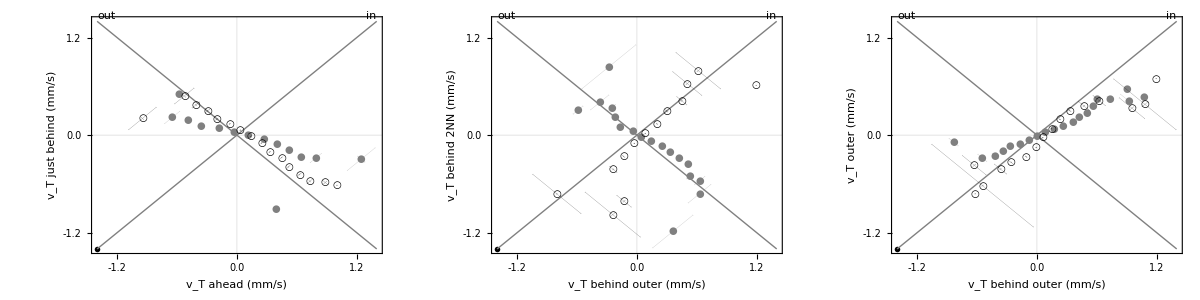
○ Layer-by-layer  ● Bath
-Graphics-

```mathematica
ft = ticksfunc[{{-2.4, 2.4}}, 6*10^-1, 0.1];
l =1.4;
papervv1 = columnexp[plotijgrid[tpvv1&,{{13, 15}, {17, 23}, {17, 25}}, True&, -Pi/4&, {"out", "in", "out", "in"}&,  vtlabel[btregion[#]]&, vtlabel[btregion[#]]&, kbt, {{-l, l}, {-l, l}}&, ft&, 0, True]]
```

```mathematica
Export["figures\\vv.pdf", papervv1];
```

#### averaged over lines

```mathematica
iilist2 =  Range[10,28,2];
ilist2 = Flatten[Table[Table[{iilist2[[i]],iilist2[[j]]},{i,j-1}], {j,Length[iilist2]}],1];
```

```mathematica
tpvvave = tplist[combinetable,ilist2, True];
Export["corrpoints\\vvavepoints.txt", ToString[tpvvave]];
```

```mathematica
tpvvave = tplist2[combinetable,ilist2, True];
Export["corrpoints\\vvavepoints2.txt", ToString[tpvvave]];
```

```mathematica
tpvvave = ToExpression[Import["corrpoints\\vvavepoints2.txt"]];
```

```mathematica
ft = ticksfunc[{{-0.9, 0.9}}, 6*10^-1, 0.1];
tab = plotlist[tpvvave&, iilist2, iilist2, True&, -Pi/4&, 4, {"out", "in", "out", "in"}&, vtlabel[ctregion[#]]&, vtlabel[ctregion[#]]&, kcombine,  {{-1, 1}, {-1, 1}}&, ft];
gridvvave = pl2grid[tab];
Print[Export["figures\\vvavecorr.pdf",columnexp[gridvvave]]];
tab2 = Partition[Partition[Select[Flatten[tab], !NumberQ[#]&], UpTo[4]], UpTo[5]];
Do[
Print[Export["figures\\vvavecorr"<>ToString[i]<>".pdf", columnexp[pl2grid[tab2[[i]]]]]];
,{i, Length[tab2]}]
```

figures\vvavecorr.pdf

figures\vvavecorr1.pdf

figures\vvavecorr2.pdf

figures\vvavecorr3.pdf

### dist-dist

#### absolute position-width, not averaged over lines

```mathematica
ilist3 = {31,49, 55, 74};
jlist3 = {35, 53, 59, 76};
ijlist3= Flatten[Table[Table[{i,j},{i, ilist3}], {j,jlist3}],1];
```

```mathematica
tppwabs = tplist[bigtable2,ijlist3, True];
Export["corrpoints\\poswidthabspoints.txt", ToString[tppwabs]];
tppwabs2 = tplist[bigtable2,ijlist3, False];
Export["corrpoints\\poswidthabspoints2.txt", ToString[tppwabs2]];
```

```mathematica
tppwabs = tplist2[bigtable2,ijlist3, True];
Export["corrpoints\\poswidthabspoints3.txt", ToString[tppwabs]];
tppwabs2 = tplist2[bigtable2,ijlist3, False];
Export["corrpoints\\poswidthabspoints4.txt", ToString[tppwabs2]];
```

```mathematica
tppwabs = ToExpression[Import["corrpoints\\poswidthabspoints3.txt"]];
tppwabs2 = ToExpression[Import["corrpoints\\poswidthabspoints4.txt"]];
```

```mathematica
ft = ticksfunc[{{-1, 1}}, 2*10^-1, 0.1];
gridppwabs = pl2grid[plotlist[tppwabs&, ilist3, jlist3, False&, -Pi/4&, 4,  {"out", "in", "narrow", "wide"}&,  absdist[#, True, True]&, absdist[#, True, True]&, kbt, {{-0.5, 0.5}, {0.6, 1}}&, ft]];
Export["figures\\poswidthcorrabs.pdf", columnexp[gridppwabs]]
gridppwabs2 = pl2grid[plotlist[tppwabs2&, ilist3, jlist3, False&, 0&, 4,  {"out", "in", "narrow", "wide"}&,  absdist[#, True, True]&, absdist[#, True, True]&, kbt, {{-0.5, 0.5}, {0.6, 1}}&, ft]];
Export["figures\\poswidthcorrabs2.pdf", columnexp[gridppwabs2]]
```

figures\poswidthcorrabs.pdf

figures\poswidthcorrabs2.pdf

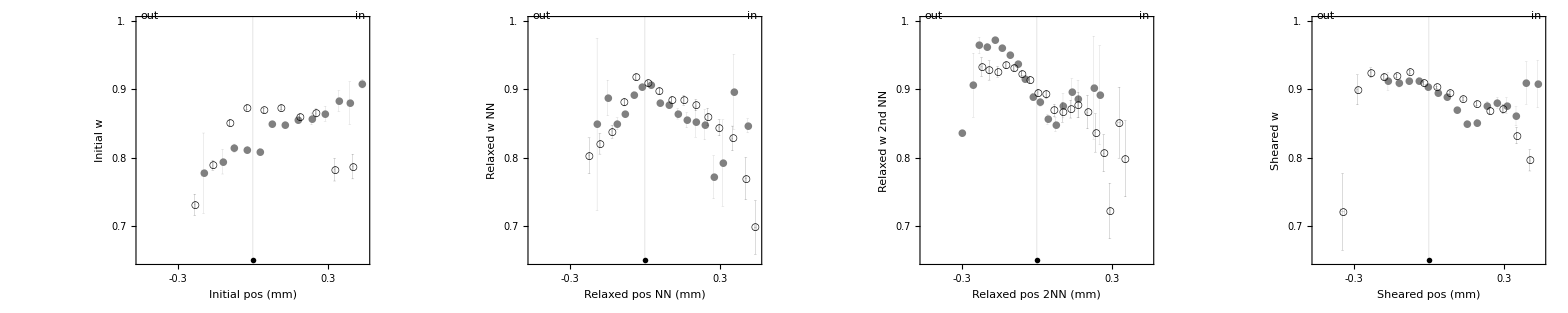
○ Layer-by-layer  ● Bath
-Graphics-

```mathematica
ft = {ticksfunc[{{0.6, 1}},0.1, 0.02][[1]], ticksfunc[{{-0.9, 0.9}}, 3*10^-1, 0.05][[1]]};paperppwabs = columnexp[plotijgrid[tppwabs2&, {{31, 35}, {49, 53}, {55, 59}, {74, 76}}, False&, 0&,  {"out", "in", "narrow", "wide"}&, absdist[#,True, True]&, absdist[#, True,False]&, kbt, {{-0.45,0.45}, {0.65, 1}}&, ft&, 0, False]]
```

```mathematica
Export["figures\\poswidthabs.pdf", paperppwabs];
```

#### absolute position-position, not averaged over lines

```mathematica
ilist4 = {31,49, 55, 74};
jlist4 = {31,49, 55, 74};
ijlist4 = Flatten[Table[Table[{ilist4[[ii]],jlist4[[jj]]},{ii,jj-1}], {jj, Length[jlist4]}],1];
```

```mathematica
tpppabs = tplist[bigtable2,ijlist4, True];
Export["corrpoints\\posposabspoints.txt", ToString[tpppabs]];
```

```mathematica
tpppabs = tplist2[bigtable2,ijlist4, True];
Export["corrpoints\\posposabspoints2.txt", ToString[tpppabs]];
```

```mathematica
tpppabs = ToExpression[Import["corrpoints\\posposabspoints2.txt"]];
```

```mathematica
ft = ticksfunc[{{-1.2, 1.2}}, 6*10^-1, 0.1];
l = 0.8;
gridpppabs = pl2grid[plotlist[tpppabs&, ilist4, jlist4, True&, -Pi/4&, 4,   {"out", "in", "out", "in"}&,  absdist[#, True, True]&, absdist[#, True, True]&, kbt, {{-l, l}, {-l, l}}&, ft]];
Export["figures\\posposcorrabs.pdf", columnexp[gridpppabs]]
```

figures\posposcorrabs.pdf

#### absolute width-width, not averaged over lines

```mathematica
ilist5 = {35, 53, 59, 76};
jlist5 = {35, 53, 59, 76};
ijlist5 = Flatten[Table[Table[{ilist5[[ii]],jlist5[[jj]]},{ii,jj-1}], {jj, Length[jlist5]}],1];
```

```mathematica
tpwwabs = tplist[bigtable2,ijlist5, True];
Export["corrpoints\\widthwidthabspoints.txt", ToString[tpwwabs]];
```

```mathematica
tpwwabs = tplist2[bigtable2,ijlist5, True];
Export["corrpoints\\widthwidthabspoints2.txt", ToString[tpwwabs]];
```

```mathematica
tpwwabs = ToExpression[Import["corrpoints\\widthwidthabspoints2.txt"]];
```

```mathematica
ft = Automatic;
gridwwabs= pl2grid[plotlist[tpwwabs&, ilist5, jlist5, True&, -Pi/4&, 4,    {"narrow", "wide", "narrow", "wide"}&,  absdist[#, True, True]&, absdist[#, True, True]&, kbt, {{0.6, 1}, {0.6, 1}}&, ft]];
Export["figures\\widthwidthcorrabs.pdf", columnexp[gridwwabs]]
```

figures\widthwidthcorrabs.pdf

#### relative position-width, averaged over lines

```mathematica
ilist6 = Range[30,48,6];
jlist6 = Range[34, 52, 6];
ijlist6 = Flatten[Table[Table[{ilist6[[ii]],jlist6[[jj]]},{ii,Length[ilist6]}], {jj, Length[jlist6]}],1];
```

```mathematica
tppwrel = tplist[combinetable,ijlist6, True];
Export["corrpoints\\poswidthrelpoints.txt", ToString[tppwrel]];
```

```mathematica
tppwrel2 = tplist[combinetable,ijlist6,False];
Export["corrpoints\\poswidthrelpoints2.txt", ToString[tppwrel2]];
```

```mathematica
tppwrel = tplist2[combinetable,ijlist6, True];
Export["corrpoints\\poswidthrelpoints3.txt", ToString[tppwrel]];
tppwrel2 = tplist2[combinetable,ijlist6,False];
Export["corrpoints\\poswidthrelpoints4.txt", ToString[tppwrel2]];
```

```mathematica
tppwrel = ToExpression[Import["corrpoints\\poswidthrelpoints3.txt"]];
tppwrel2 = ToExpression[Import["corrpoints\\poswidthrelpoints4.txt"]];
```

```mathematica
ft = ticksfunc[{{-1.2, 1.2}}, 6*10^-1, 0.1];
l = 0.6;
gridpwrel= pl2grid[plotlist[tppwrel&, ilist6, jlist6, #2==34&, -Pi/4&, 4,  {"out", "in", "narrow", "wide"}&, reldist[#, True,False, False]&, reldist[#, True, False, False]& , kcombine,{{-l,l},If[#2==34,  {0.6, 1}, {-l, l}]}&, ft]];
Export["figures\\poswidthcorrrel.pdf", columnexp[gridpwrel]]
gridpwrel2= pl2grid[plotlist[tppwrel2&, ilist6, jlist6, #2≠ 34&,0&, 4,  {"out", "in", "narrow", "wide"}&, reldist[#, True,False, False]&, reldist[#, True, False, False]& , kcombine,{{-l,l},If[#2==34,  {0.6, 1}, {-l, l}]}&, ft]];
Export["figures\\poswidthcorrrel2.pdf", columnexp[gridpwrel2]]
```

figures\poswidthcorrrel.pdf

figures\poswidthcorrrel2.pdf

```mathematica
(*ft = ticksfunc[{{-1, 1}}, 0.2, 0.05];
ft2 = ticksfunc[{{-1, 1}}, 0.1, 0.05];
ft = {ft2[[1]], ft[[1]]};
pr = Switch[#1, 30, {{-0.29, 0.29}, {0.65, 1}}, 36, {{-0.45, 0.3}, {-0.13, 0.13}}, 42, {{-0.5, 0.25},{-0.3, 0.15}}, 48, {{-0.25, 0.35}, {-0.1, 0.15}}]&;
paperpwrel = plotijgrid[If[#1>0, tppwrel2, tppwrel]&,{{30, 34}, {36, 40}, {42, 46}, {48, 52}}, False&, If[#1>0 , 0 , -Pi/4]&,  {"out", "in", "narrow", "wide"}&,  reldist[#,True, True, False]&, reldist[#, True, False, False]& , kcombine,  pr, ft&, 4, False]*)
```

#### relative position-position, averaged over lines

```mathematica
ilist7 = Range[30,48,6];
jlist7 = ilist7;
ijlist7 = Flatten[Table[Table[{ilist7[[ii]],jlist7[[jj]]},{ii,jj-1}], {jj, Length[jlist7]}],1];
```

```mathematica
tppprel = tplist[combinetable,ijlist7, True];
Export["corrpoints\\posposrelpoints.txt", ToString[tppprel]];
```

```mathematica
tppprel = tplist2[combinetable,ijlist7, True];
Export["corrpoints\\posposrelpoints2.txt", ToString[tppprel]];
```

```mathematica
tppprel  = ToExpression[Import["corrpoints\\posposrelpoints2.txt"]];
```

```mathematica
ft = ticksfunc[{{-1.2, 1.2}}, 6*10^-1, 0.1];
l = 0.8;
gridpprel= pl2grid[plotlist[tppprel&, ilist7, jlist7, True&, -Pi/4&, 4,   {"out", "in", "out", "in"}&, reldist[#, True, True, False]&, reldist[#, True, True, False]& , kcombine,{{-l, l},{-l,l}}&, ft]];
Export["figures\\posposcorrrel.pdf", columnexp[gridpprel]]
```

figures\posposcorrrel.pdf

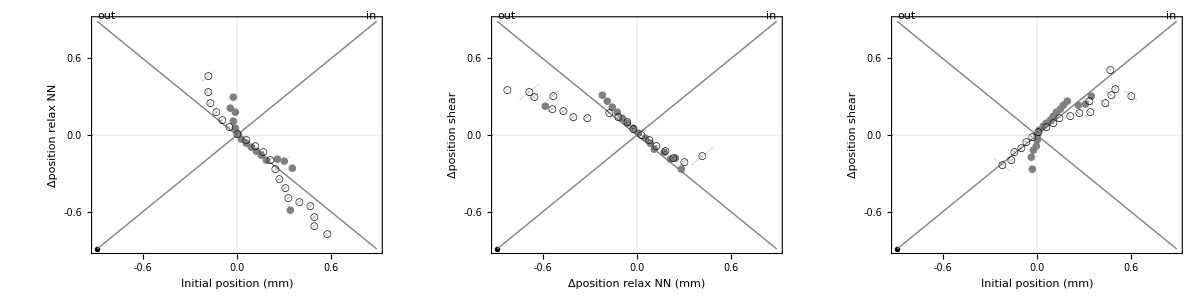

```mathematica
ft = ticksfunc[{{-1.2, 1.2}}, 3*10^-1, 0.1];
px = 0.89;
paperpprel = plotijgrid[tppprel&,{{30, 36}, {36, 48}, {30, 48}}, True&, -Pi/4&,  {"out", "in", "out", "in"}&,  reldist[#,False, True, False]&, reldist[#, False, False, False]& , kcombine,  {{-px, px},{-px, px}}&, ft&, 0, True]
```

#### relative width-width, averaged over lines

```mathematica
ilist8 =Range[34, 52, 6];
jlist8 = ilist8;
ijlist8 = Flatten[Table[Table[{ilist8[[ii]],jlist8[[jj]]},{ii,jj-1}], {jj, Length[jlist8]}],1];
```

```mathematica
tpwwrel = tplist[combinetable,ijlist8, True];
Export["corrpoints\\widthwidthrelpoints.txt", ToString[tpwwrel]];
```

```mathematica
tpwwrel2 = tplist[combinetable,ijlist8, False];
Export["corrpoints\\widthwidthrelpoints2.txt", ToString[tpwwrel2]];
```

```mathematica
tpwwrel3 = tplist2[combinetable, ijlist8, True];
Export["corrpoints\\widthwidthrelpoints3.txt", ToString[tpwwrel3]];
tpwwrel4 = tplist2[combinetable, ijlist8, False];
Export["corrpoints\\widthwidthrelpoints4.txt", ToString[tpwwrel4]];
```

```mathematica
tpwwrel  = ToExpression[Import["corrpoints\\widthwidthrelpoints3.txt"]];
tpwwrel2 = ToExpression[Import["corrpoints\\widthwidthrelpoints4.txt"]];
```

```mathematica
ft = ticksfunc[{{-1, 1}}, 2*10^-1, 0.1];
gridwwrel= pl2grid[plotlist[If[#1==34, tpwwrel2, tpwwrel]&, ilist8, jlist8, #1>34&, If[#1==34, 0, -Pi/4]&, 4,  {"narrow", "wide", "narrow", "wide"}&, reldist[#, True, True, False]&, reldist[#, True, True, False]& , kcombine,{If[#1==34,  {0.6, 1}, {-0.3, 0.3}],If[#2==34,  {0.6, 1}, {-0.3, 0.3}]}&, ft]];
Export["figures\\widthwidthcorrrel.pdf", columnexp[gridwwrel]]
```

figures\widthwidthcorrrel.pdf

```mathematica
tpwwrel4052 = tplist2[Select[combinetable, -0.35<#[[40]]<0.35 && -0.35<#[[52]]<0.35&], {{40, 52}}, True];
```

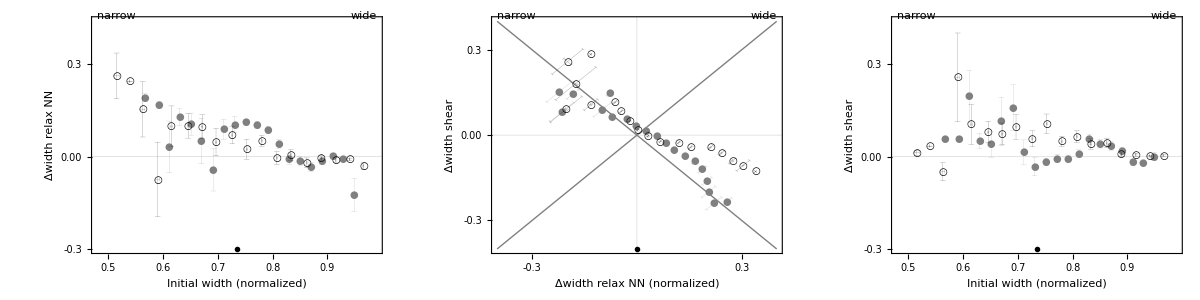

```mathematica
px = 0.35;
paperwwrel = plotijgrid[If[#1==34, tpwwrel2, tpwwrel4052]&
,{{34, 40} ,{40, 52}, {34, 52}}
, #1==40&
,  If[#1==34, 0, -Pi/4]&, {"narrow", "wide", "narrow", "wide"}&
,  reldist[#,False, True, False]&
, reldist[#, False, False, False]& 
, kcombine
,  If[#1==34,  {{0.48,0.99}, {-0.3, 0.44}}, {{-0.4, 0.4}, {-0.4, 0.4}}]&
,{ticksfunc[{{-0.6, 1.2}}, If[#1==34, 0.15, 0.3], 0.05][[1]], If[#1==34, ticksfunc[{{0.5, 0.9}},0.1, 0.05],ticksfunc[{{-0.9, 0.9}},3*10^-1, 0.05]][[1]]}&
, 3, False]
```

```mathematica
Export["figures\\distdistrel.pdf", Column[{plegend[Row], paperpprel, paperwwrel}, Alignment->Right]];
```

### vector-distribution

#### vector - absolute distribution

```mathematica
ilist9 = Range[11, 29, 2];
jlist9 = {31,49, 55, 74, 35, 53, 59, 76} ;
ijlist9 = Flatten[Table[Table[{ilist9[[ii]],jlist9[[jj]]},{ii,Length[ilist9]}], {jj, Length[jlist9]}],1];
```

```mathematica
tpvdabs = tplist[bigtable2,ijlist9, True];
Export["corrpoints\\vdistabspoints.txt", ToString[tpvdabs]];
```

```mathematica
tpvdabs = tplist2[bigtable2,ijlist9, False];
Export["corrpoints\\vdistabspoints2.txt", ToString[tpvdabs]];
```

```mathematica
tpvdabs = ToExpression[Import["corrpoints\\vdistabspoints2.txt"]];
```

```mathematica
ft1 = ticksfunc[{{-1.2, 1.2}},1*10^-1, 0.01];
ft2 = ticksfunc[{{-1.2, 1.2}}, 3*10^-1, 0.1];
ft = {ft2[[1]], ft1[[1]]};
l = 0.5;
ii = 1;
Do[
If[jlist[[1]]==31
, ft = {ft1[[1]] ,ft2[[1]]}
,ft = {ft1[[1]], ft2[[1]]};
];
tab = plotlist[tpvdabs&, ilist, jlist, (*!MemberQ[{35, 53, 59, 76}, #2]*)False&, (* -Pi/4*)0&, 4,  {"out", "in", If[MemberQ[{35, 53, 59, 76}, #2],"narrow", "out"], If[MemberQ[{35, 53, 59, 76}, #2],"wide", "in"]}&,  vtlabel[btregion[#]]&, absdist[#, True, True]&, kbt, {{-l, l}, If[MemberQ[{35, 53, 59, 76}, #2],  {0.75, 1}, {-0.15, 0.15}]}&, ft];
Export["figures\\vdistcorrabs"<>ToString[ii]<>".pdf", columnexp[pl2grid[tab]]];
ii = ii+1;
,{ilist, {ilist9[[1;;5]], ilist9[[6;;]]}}, {jlist, {jlist9[[1;;4]], jlist9[[5;;]]}}];
```

#### vector - relative distribution

```mathematica
ilist10 = Range[10, 28, 2];
jlist10 = Join[Range[30,48,6], Range[34, 52, 6]];
ijlist10 = Flatten[Table[Table[{ilist10[[ii]],jlist10[[jj]]},{ii,Length[ilist10]}], {jj, Length[jlist10]}],1];
```

```mathematica
tpvdrel = tplist[combinetable,ijlist10, True];
Export["corrpoints\\vdistrelpoints.txt", ToString[tpvdrel]];
```

```mathematica
tpvdrel = tplist2[combinetable,ijlist10, False];
Export["corrpoints\\vdistrelpoints2.txt", ToString[tpvdrel]];
```

```mathematica
tpvdrel = ToExpression[Import["corrpoints\\vdistrelpoints2.txt"]];
```

```mathematica
ft1 = ticksfunc[{{-1.2, 1.2}},3*10^-1, 0.1];
ft2 = ticksfunc[{{-1.2, 1.2}}, 3*10^-1, 0.1];
ft = {ft2[[1]], ft1[[1]]};
l = 0.3;
ii = 1;
Do[
tab = plotlist[tpvdrel&, ilist, jlist, #2>34&, (* -Pi/4*)0&, 4,  {"out", "in", If[MemberQ[Range[34, 52, 6], #2],"narrow", "out"], If[MemberQ[Range[34, 52, 6], #2],"wide", "in"]}&,  vtlabel[ctregion[#]]&,  reldist[#, True, True, False]&,kcombine, {{-l, l}, If[#2==34,  {0.5, 1}, {-l, l}]}&, ft];
Export["figures\\vdistcorrrel"<>ToString[ii]<>".pdf", columnexp[pl2grid[tab]]];
ii = ii+1;
,{ilist, {ilist10[[1;;5]], ilist10[[6;;]]}}, {jlist, {jlist10[[1;;4]], jlist10[[5;;]]}}];
```